This works for the searches made with the 30minute incrament.

```mathematica
ClearAll["Global`*"]
```

```mathematica
tag ={"#boston","#bostonmarathon","#bostonstrong","#prayforboston"};
S[x_]:=StringSplit[StringReplace[x,{"\""->""}]," -> "];
Fdate[x_]:=DateString[{2013,4,15,(5+x),0,0},{"DayNameShort","Hour12","AMPMLowerCase"}];
```

```mathematica
L=96;
For[n=1,n≤4,n++,
For[i=1,i≤L,i++,

file="/Users/danielgladstone/Documents/twitter_project/auto_graphing/"<>tag[[n]]<>"1039"<>"/"<>Fdate[i];

If[FileExistsQ[file],

F =Import[file,"List"];

GList[tag[[n]]][i]=DeleteDuplicates[Table[
joined=First[S[F[[j]]]]->Last[S[F[[j]]]]
,{j,1,Length[F]}]];
If[Length[GList[tag[[n]]][i]]≤1,

(*Print["Zero: n="<>ToString[n]<>". i="<>ToString[i]];*)

G[tag[[n]]][i]=0;
G[VC][tag[[n]]][i]=0;
G[VID][tag[[n]]][i]=0;
G[CC][tag[[n]]][i]=0;
G[GD][tag[[n]]][i]=0;
G[GR][tag[[n]]][i]=0;
G[GCC][tag[[n]]][i]=0;
G[GA][tag[[n]]][i]=0;
G[MND][tag[[n]]][i]=0;
G[MDC][tag[[n]]][i]=0;,

G[tag[[n]]][i]=Graph[GList[tag[[n]]][i]];
G[VC][tag[[n]]][i]=VertexCount[G[tag[[n]]][i]];
G[VID][tag[[n]]][i]=Mean[VertexInDegree[G[tag[[n]]][i]]];
G[CC][tag[[n]]][i]=Mean[ClosenessCentrality[G[tag[[n]]][i]]];
G[GD][tag[[n]]][i]=GraphDensity[G[tag[[n]]][i]];
G[GR][tag[[n]]][i]=GraphReciprocity[G[tag[[n]]][i]];
G[GCC][tag[[n]]][i]=GlobalClusteringCoefficient[G[tag[[n]]][i]];
G[GA][tag[[n]]][i]=GraphAssortativity[G[tag[[n]]][i]];
G[MND][tag[[n]]][i]=Mean[MeanNeighborDegree[G[tag[[n]]][i]]];
G[MDC][tag[[n]]][i]=Mean[MeanDegreeConnectivity[G[tag[[n]]][i]]];
];
,
G[tag[[n]]][i]=0;
G[VC][tag[[n]]][i]=0;
G[VID][tag[[n]]][i]=0;
G[CC][tag[[n]]][i]=0;
G[GD][tag[[n]]][i]=0;
G[GR][tag[[n]]][i]=0;
G[GCC][tag[[n]]][i]=0;
G[GA][tag[[n]]][i]=0;
G[MND][tag[[n]]][i]=0;
G[MDC][tag[[n]]][i]=0;]
]]
```

```mathematica
type={VC,VID,CC,GD,GR,GCC,GA,MND,MDC};

For[p=1,p≤9,p++,

GType=type[[p]];

data=
Table[
Table[
G[GType][tag[[n]]][i],{i,L}]
,{n,1,4}(*slect what hashtags to see here i.e.#prayforboston is (n,4,4)*)
];

d[type[[p]]]=data;
]
```

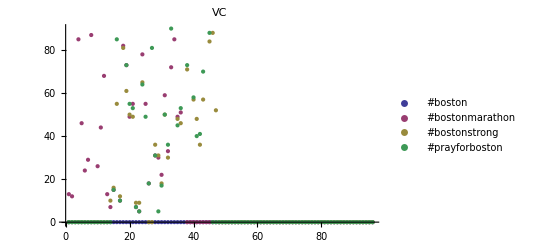
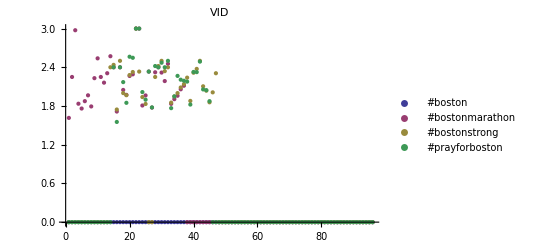
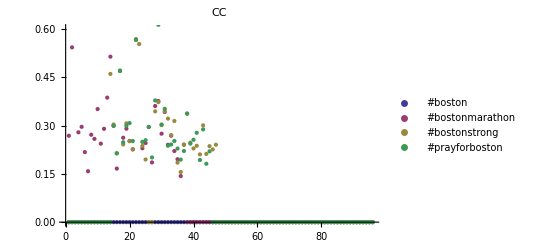
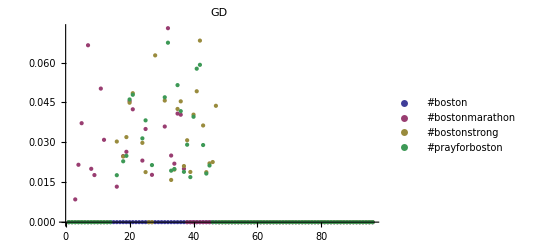
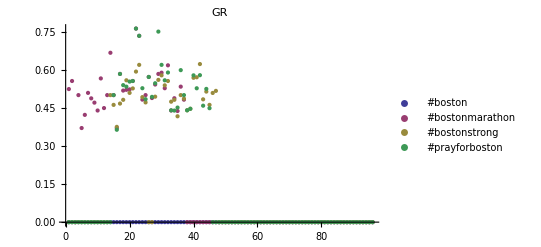
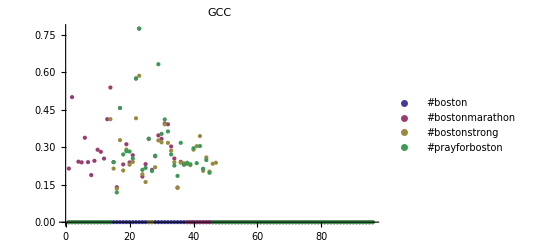
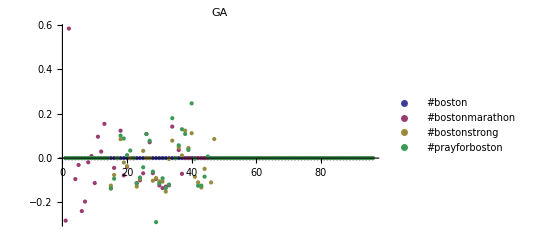
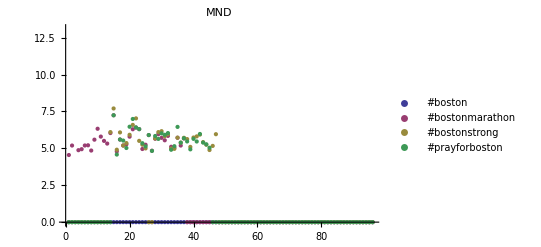

{0.,65.4748-0.892092 x,36.423-0.368258 x,36.9844-0.389928 x}

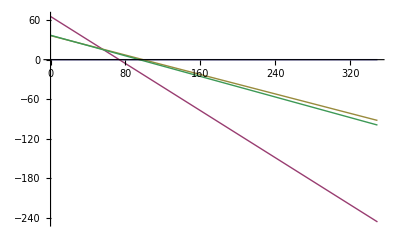

```mathematica
lp=Table[ListPlot[d[type[[o]]],PlotLabel->type[[o]], PlotLegends->Table[
tag[[t]],{t,1,4}]]
,{o,9}]

md=Table[Fit[d[type[[1]]][[j]],{1,x},x],{j,4}]

min=Min[Table[d[type[[1]]][[j]],{j,4}]];
max = Max[Table[d[type[[1]]][[j]],{j,4}]];
Plot[md,{x,min,max}]

(*
Table[
d[type[[1]]][[j]],{j,4}];

Show[lp,Plot[md,{x,min,max}]]*)
```

```mathematica
VertexInDegree[G[tag[[3]]][2]]
```

{}

```mathematica
.
```

```mathematica
G=Graph[GList]

VertexCount[G]
Mean[VertexInDegree[G]]
Mean[ClosenessCentrality[G]]
GraphDensity[G]
GraphReciprocity[G]
GlobalClusteringCoefficient[G]
GraphAssortativity[G]
Mean[MeanNeighborDegree[G]]
Mean[MeanDegreeConnectivity[G]]
```

-Graphics-

4

2

0.9375

2/3

3/4

3/5

0

9/2

7/3

```mathematica
First[F[[1]]]->Last[F[[1]]]
```

#cat→#cats

```mathematica
.
```

```mathematica
Table[
Print[i];
,{i,2,5}]
```

2

3

4

5

{Null,Null,Null,Null}